```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->False,FrameTicks->{Automatic,Automatic}];
```

```mathematica
importTHP=Transpose[Import["/Users/gabrielpatenotte/Desktop/Wavemeter 8-starts-2021-11-13-00-00-00-ends-2021-11-15-10-17-32.csv",{"Data",2;;}]];
Print[StringForm["The first data point occurs at ``, last at ``",importTHP[[1,1]],importTHP[[1,-1]]]]
timeTHP=AbsoluteTime/@importTHP[[1]];
timeTHP=timeTHP-timeTHP[[1]];
```

The first data point occurs at 2021-11-13 00:00:00, last at 2021-11-15 10:17:00

```mathematica
{T,H,P}=importTHP[[2;;-1]];
ftoC[x_]=(x-32)5/9+273.15;
T=Map[ftoC,T];
P=25.4*P;
```

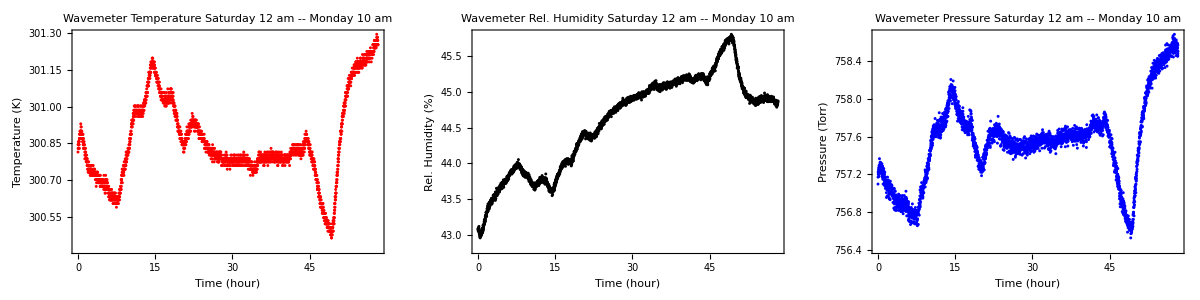

```mathematica
TableForm[{Table[ListPlot[Transpose@{timeTHP/3600,x[[1]]},ImageSize->Large,PlotStyle->x[[2]],PlotLabel-> StringForm["Wavemeter ``\n Saturday 12 am -- Monday 10 am",x[[3]]],FrameLabel->{"Time (hour)",x[[3]]<>x[[4]]}],{x,{{T,Red,"Temperature"," (K)"},{H,Black,"Rel. Humidity"," (%)"},{P,Blue, "Pressure"," (Torr)"}}}]}]
```

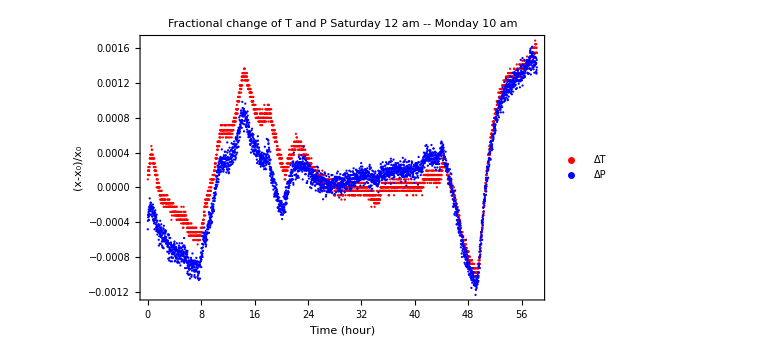
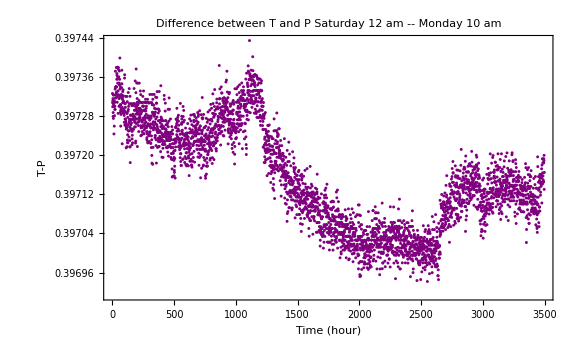
-Graphics- | -Graphics-

```mathematica
TableForm[{{ListPlot[Table[Transpose@{timeTHP/3600,(x-x[[-1500]])/x[[-1500]]},{x,{T,P}}],ImageSize->Large,PlotLegends->{"ΔT","ΔP"},PlotLabel->"Fractional change of T and P\n Saturday 12 am -- Monday 10 am",FrameLabel->{"Time (hour)","(x-x_0)/x_0"}],ListPlot[T/P,ImageSize->Large,PlotStyle->Purple,PlotLabel->"Difference between T and P\n Saturday 12 am -- Monday 10 am",FrameLabel->{"Time (hour)","T-P"}]}}]
```

```mathematica
Correlation[T,P]
```

0.892735

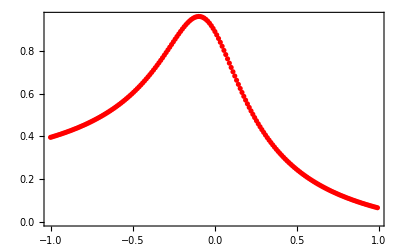

```mathematica
ListPlot[Table[{α,Correlation[T-α H,P]},{α,-1,1,.011}]]
```

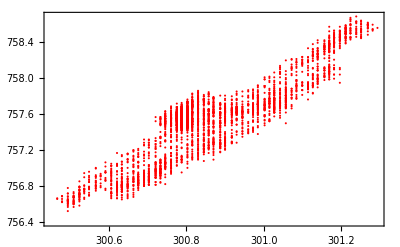

```mathematica
ListPlot[Transpose@{T,H}]
```

```mathematica
import=Import["/Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data20.csv"];
```

```mathematica
import[[All,1]][[-1]]
```

2021-11-13T20:44:57.91

```mathematica
timeS=AbsoluteTime/@importSome[[1]];
timeS=timeS-timeS[[1]];
{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S,cErrorS}=importSome[[Range[2,18,2]]];
```

```mathematica
Print[StringForm["The first data point occurs at ``, last at ``",importSome[[1,1]],importSome[[1,-1]]]]
```

The first data point occurs at 2021-11-12T19:30:00.067, last at 2021-11-13T20:43:54.014

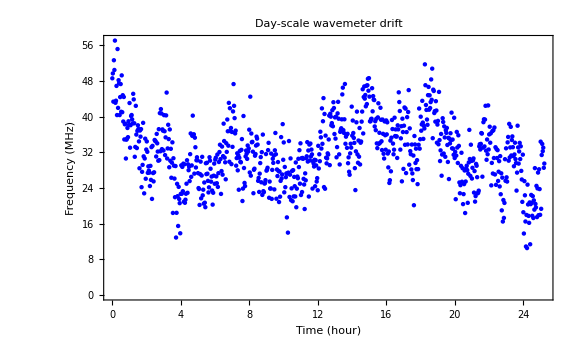

```mathematica
ListPlot[Transpose@{timeS/3600 ,1000 cErrorS},ImageSize->Large,PlotLabel->"Day-scale wavemeter drift",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Blue]
```

```mathematica
importLast=Transpose[Import["/Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data20.csv",{"Data",Range[633588,634136,1]}]];
importLast2=Transpose[Import["/Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data20.csv",{"Data",Range[633588-100000,634136-100000,1]}]];
importMid=Transpose[Import["/Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data20.csv",{"Data",Range[601256,634136,33]}]];
```

```mathematica
importDetail=Transpose[Import["/Users/gabrielpatenotte/Desktop/wm8Data20.csv",{"Data",Range[633588-59(634136-633588),634136,1]}]];
```

```mathematica
timeD=AbsoluteTime/@importDetail[[1]];
timeD=timeD-timeD[[1]];
{c1D,c2D,c3D,c4D,c5D,c6D,c7D,c8D,cErrorD}=importDetail[[Range[2,18,2]]];
```

```mathematica
timeL=AbsoluteTime/@importLast[[1]];
timeL=timeL-timeL[[1]];
{c1L,c2L,c3L,c4L,c5L,c6L,c7L,c8L,cErrorL}=importLast[[Range[2,18,2]]];
timeL2=AbsoluteTime/@importLast2[[1]];
timeL2=timeL2-timeL2[[1]];
{c1L2,c2L2,c3L2,c4L2,c5L2,c6L2,c7L2,c8L2,cErrorL2}=importLast2[[Range[2,18,2]]];
timeM=AbsoluteTime/@importMid[[1]];
timeM=timeM-timeM[[1]];
{c1M,c2M,c3M,c4M,c5M,c6M,c7M,c8M,cErrorM}=importMid[[Range[2,18,2]]];
timeS=AbsoluteTime/@importSome[[1]];
timeS=timeS-timeS[[1]];
{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S,cErrorS}=importSome[[Range[2,18,2]]];
```

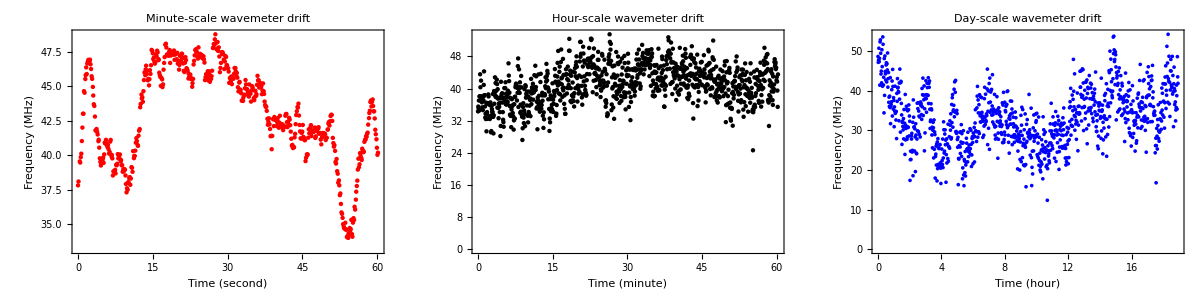

```mathematica
TableForm[{{ListPlot[Transpose@{timeL ,1000 cErrorL},ImageSize->Large,PlotLabel->"Minute-scale wavemeter drift",FrameLabel->{"Time (second)","Frequency (MHz)"},PlotStyle->Red],ListPlot[Transpose@{timeM/60 ,1000 cErrorM},ImageSize->Large,PlotLabel->"Hour-scale wavemeter drift",FrameLabel->{"Time (minute)","Frequency (MHz)"},PlotStyle->Black],ListPlot[Transpose@{timeS/3600 ,1000 cErrorS},ImageSize->Large,PlotLabel->"Day-scale wavemeter drift",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Blue]}}]
```

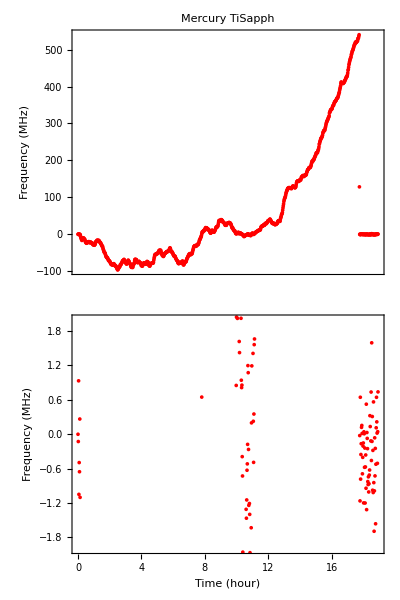
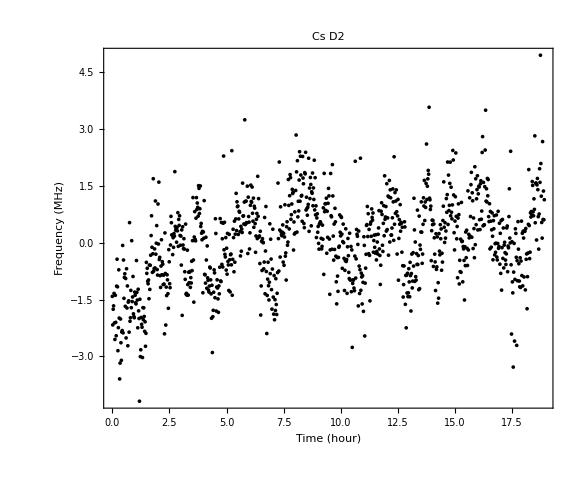
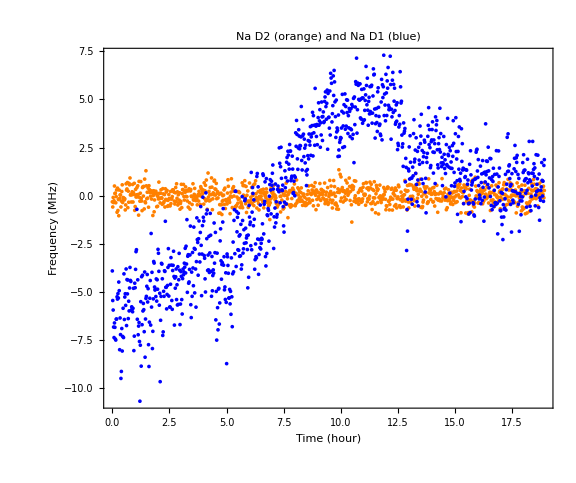
-Graphics- | -Graphics- | -Graphics-

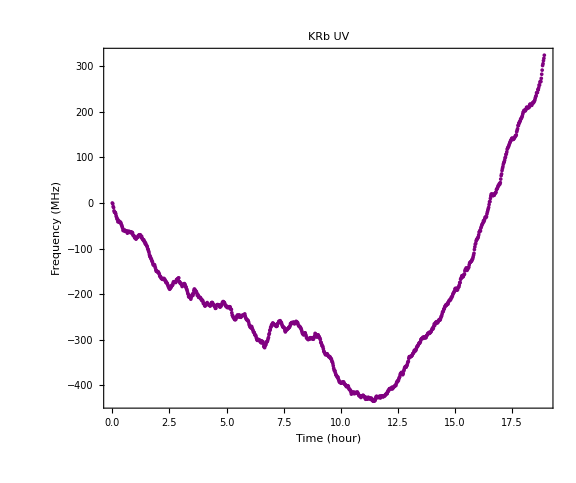

```mathematica
TableForm[{{{ListPlot[Transpose@{timeS/3600,1000(c1S-c1S[[1]])},ImageSize->Large,ImagePadding-> {{65,10},{0,0}},PlotLabel->"Mercury TiSapph",FrameLabel->{,"Frequency (MHz)"},PlotStyle->Red,FrameTicks->{{True,False},{False,False}}],ListPlot[Transpose@{timeS/3600,1000(c1S-c1S[[1]])},ImageSize->Large,ImagePadding-> {{65,10},{50,25}},PlotRange->{-2,2},FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Red,AspectRatio->1/6]},ListPlot[Transpose@{timeS/3600,1000(c2S-Mean[c2S])},ImageSize->Large,ImagePadding-> {{65,10},{50,0}},PlotLabel->"Cs D2",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Black,AspectRatio->.84],ListPlot[{Transpose@{timeS/3600,1000(c3S-Mean[c3S])},Transpose@{timeS/3600,1000(c4S-Mean[c4S])}},ImageSize->Large,ImagePadding-> {{65,10},{50,0}},PlotLabel->"Na D2 (orange) and Na D1 (blue)",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->{Orange,Blue},AspectRatio->.84,PlotRange->All]}},TableSpacing->{0, 0}]
TableForm[{{ListPlot[Transpose@{timeS/3600,1000(c8S-c8S[[1]])},ImageSize->Large,ImagePadding-> {{65,10},{50,0}},PlotLabel->"KRb UV",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Purple,AspectRatio->.84]}},TableSpacing->{0, 0}]
```

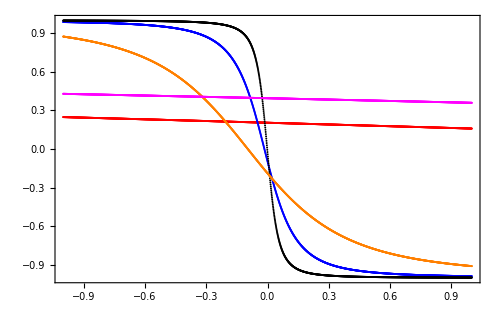
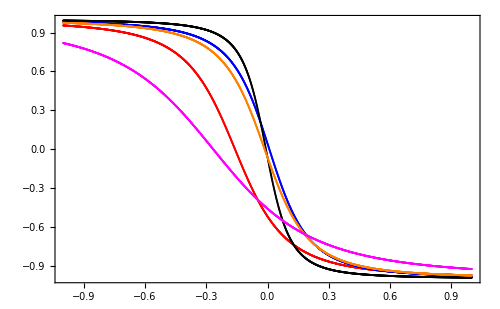
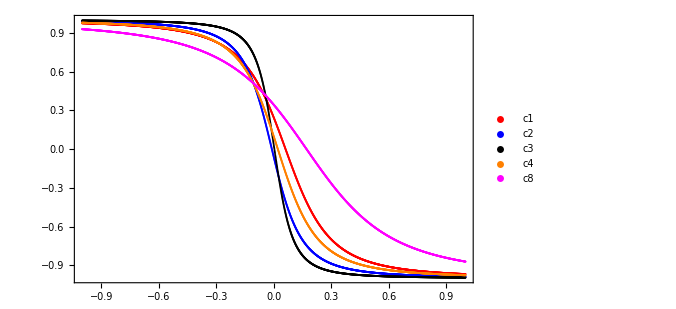

```mathematica
{ListPlot[Table[Table[{α,Correlation[x-α cErrorS,cErrorS]},{α,-1,1,.001}],{x,{c1S,c2S,c3S,c4S,c8S}}],ImageSize->500],ListPlot[Table[Table[{α,Correlation[x-α cErrorL,cErrorL]},{α,-1,1,.001}],{x,{c1L,c2L,c3L,c4L,c8L}}],ImageSize->500],ListPlot[Table[Table[{α,Correlation[x-α cErrorL2,cErrorL2]},{α,-1,1,.001}],{x,{c1L2,c2L2,c3L2,c4L2,c8L2}}],ImageSize->500,PlotLegends->{"c1","c2","c3","c4","c8"}]}
```

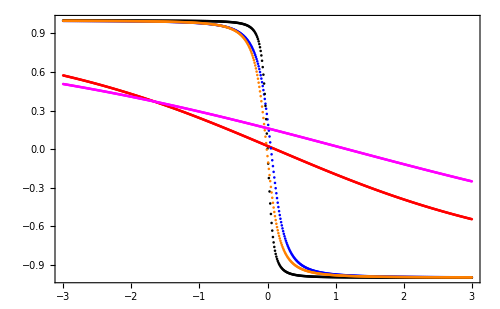

```mathematica
ListPlot[Table[Table[{α,Correlation[x-α cErrorD,cErrorD]},{α,-3,3,.01}],{x,{c1D,c2D,c3D,c4D,c8D}}],ImageSize->500]
```

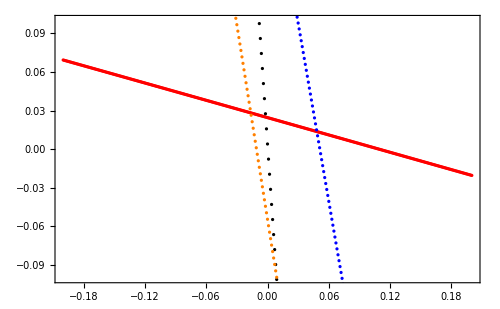

```mathematica
ListPlot[Table[Table[{α,Correlation[x-α cErrorD,cErrorD]},{α,-.2,.2,.001}],{x,{c1D,c2D,c3D,c4D,c8D}}],ImageSize->500,PlotRange->{-.1,.1}]
```

```mathematica
2 * fna/fcs
```

```mathematica
import25=Transpose[Import["/Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data25.csv",{"Data",23000;;}]];
timeS=AbsoluteTime/@import25[[1]];
timeS=timeS-timeS[[1]];
{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S,cErrorS}=import25[[Range[2,18,2]]];
```

Import::nffil: File /Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data25.csv not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partw: Part {2,4,6,8,10,12,14,16,18} of Transpose[$Failed] does not exist.

Set::shape: Lists {c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S,cErrorS} and Transpose[$Failed]⟦{2,4,6,8,10,12,14,16,18}⟧ are not the same shape.

```mathematica
Table[x[[1]],{x,{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}}]
Table[2.998 10^8/x[[1]],{x,{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}}]//Quiet
```

{353534.,0,508849.,508333.,325122.,472158.,0,328966.}

{848.009,ComplexInfinity,589.173,589.771,922.116,634.957,ComplexInfinity,911.34}

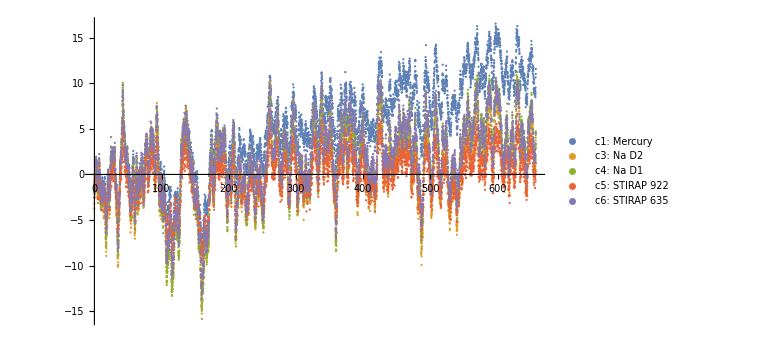

```mathematica
TableForm[ListPlot[Table[Transpose@{timeS,1000(x-x[[10]])},{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->Large,PlotRange->All,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"}]]
```

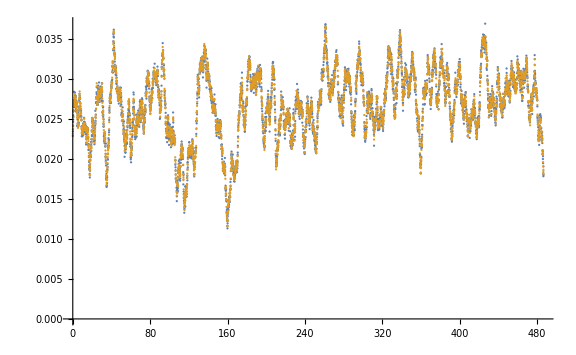

```mathematica
ListPlot[{Transpose@{timeS,c3S-508848.92},Transpose@{timeS,cErrorS}},ImageSize->Large]
```

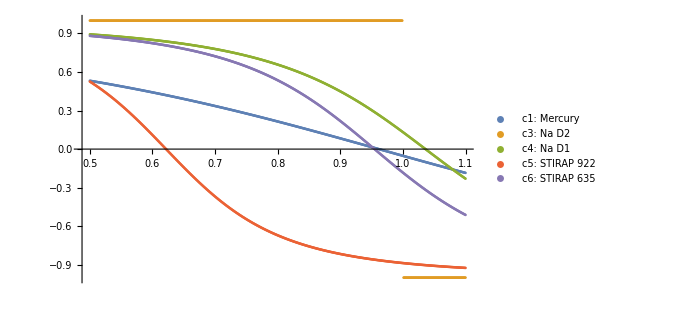

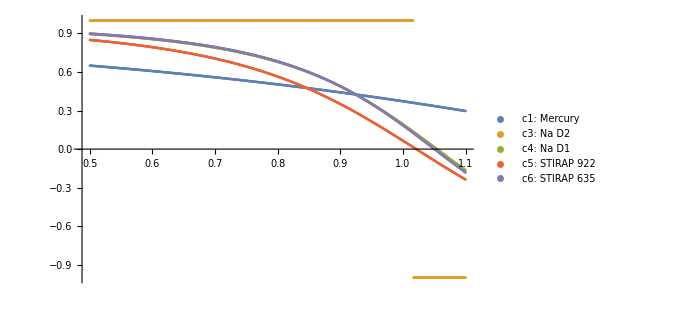

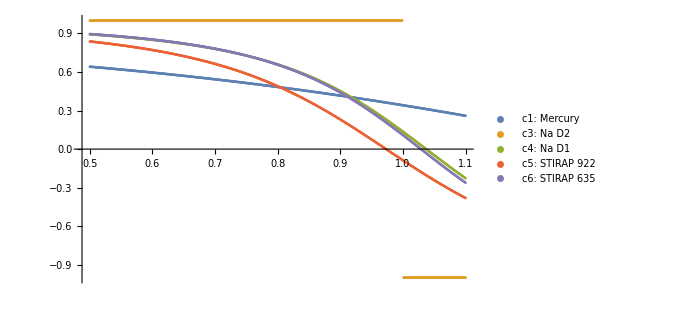

```mathematica
ListPlot[Table[Table[{α,Correlation[x-α (c3S-508848.92),(c3S-508848.92)]},{α,.5,1.1,.001}],{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->500,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"}]//Quiet
ListPlot[Table[Table[{α,Correlation[x-(-0.05474943705477249+2.0409392195194627*^-6 x[[1]])α (c3S-508848.92),(c3S-508848.92)]},{α,.5,1.1,.001}],{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->500,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"}]//Quiet
ListPlot[Table[Table[{α,Correlation[x-x[[1]]/c3S[[1]] α (c3S-508848.92),(c3S-508848.92)]},{α,.5,1.1,.001}],{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->500,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"}]//Quiet
```

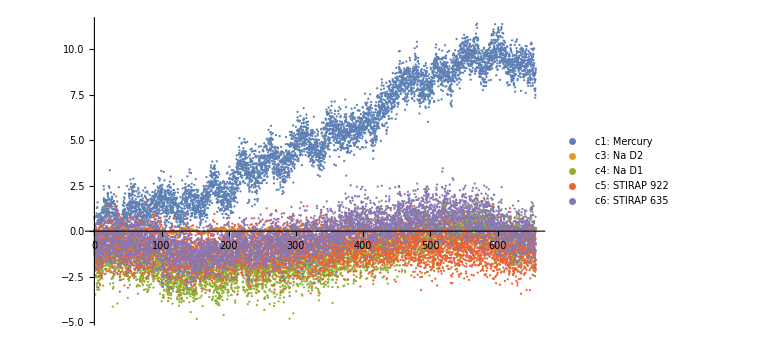

```mathematica
TableForm[ListPlot[Table[Transpose@{timeS,1000((x-(-0.05474943705477249+2.0409392195194627*^-6 x[[1]]) (c3S-508848.92))-(x[[1]]-(-0.05474943705477249+2.0409392195194627*^-6 x[[1]]) (c3S[[1]]-508848.92)))},{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->Large,PlotRange->All,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"}]]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

FittedModel[-0.0547494+2.04094×10^-6 x]

0.996609

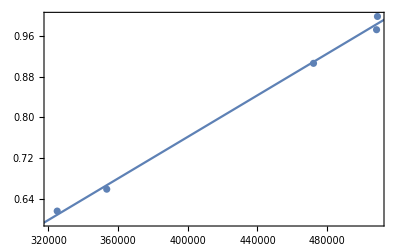

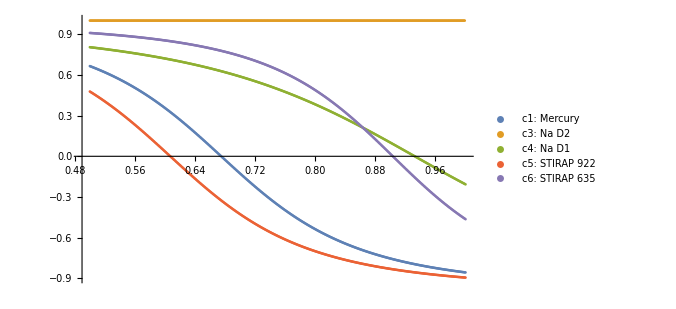

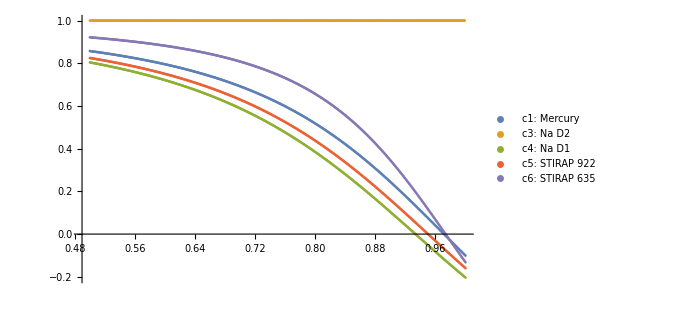

```mathematica
data=Table[{x[[1]],MinimalBy[Table[{α,Correlation[x[[1;;1800]]-α (c3S[[1;;1800]]-508848.92),(c3S[[1;;1800]]-508848.92)]^2},{α,.5,1,.001}],Last][[All,1]][[1]]},{x,{c1S,c3S,c4S,c5S,c6S}}];
lm=LinearModelFit[data,x,x]
lm["RSquared"]
Show[ListPlot[data],Plot[lm[x],{x,0,6 10^5}],Frame->True]
```

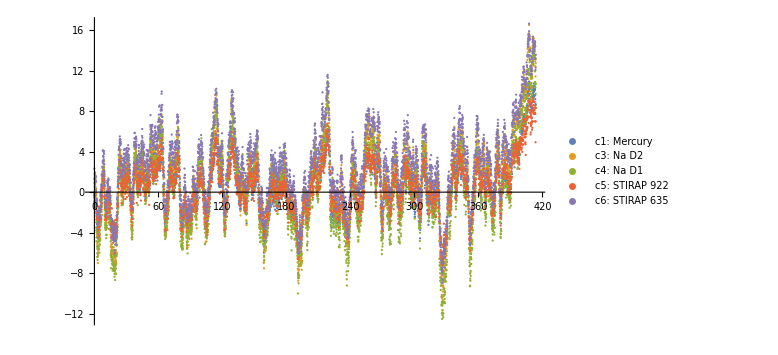

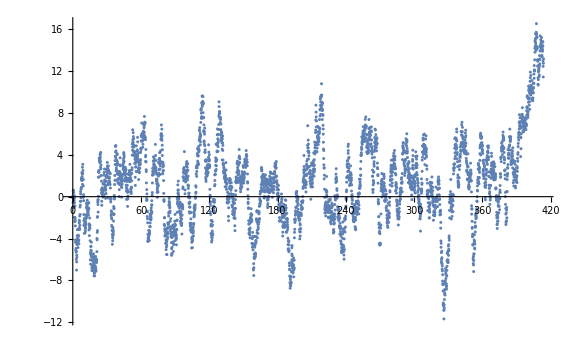
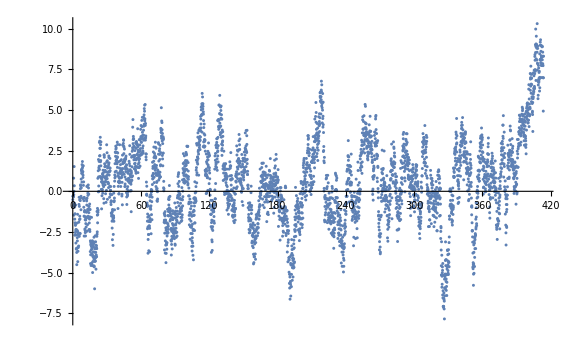
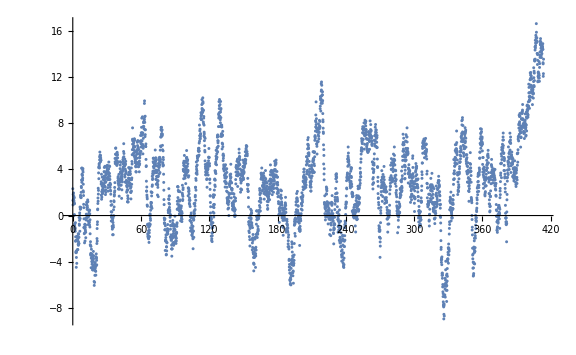

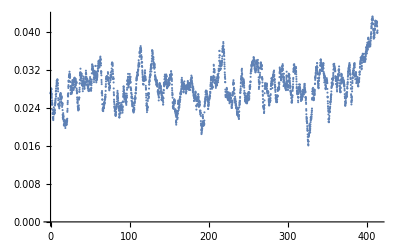

```mathematica
ListPlot[Table[Transpose@{timeS,1000(x-x[[10]])},{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->Large,PlotRange->All,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"}]
Table[ListPlot[Transpose@{timeS,1000(x-x[[10]])},ImageSize->Large,PlotRange->All],{x,{c3S,c5S,c6S}}]
ListPlot[Transpose@{timeS,cErrorS}]
```

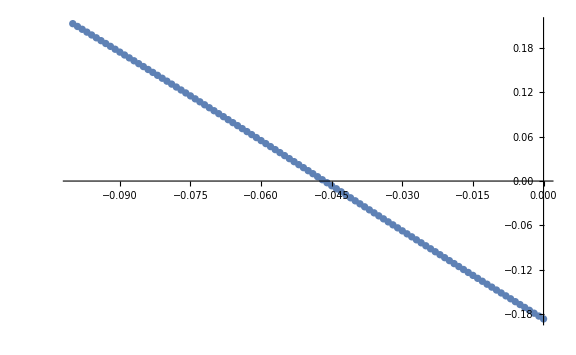
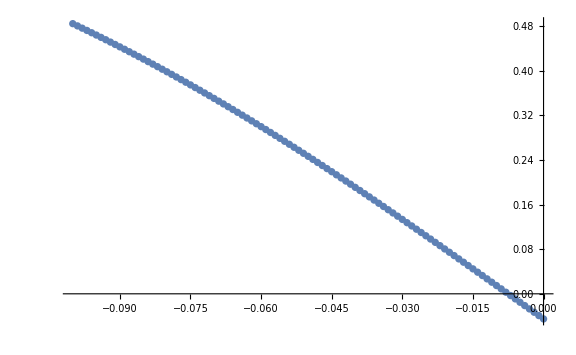

```mathematica
{ListPlot[Table[{α,Correlation[c6S-α cErrorS,cErrorS]},{α,-.1,0,.001}],ImageSize->Large],
ListPlot[Table[{α,Correlation[c5S-α cErrorS,cErrorS]},{α,-.1,0,.001}],ImageSize-> Large]}
```

```mathematica
import6=Transpose[Import["/Users/gabrielpatenotte/Desktop/wm8Data25 - Copy (3).csv",{"Data",Range[20,534000,1000]}]];
timeS=AbsoluteTime/@import6[[1]];
timeS=timeS-timeS[[1]];
{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}=import6[[Range[2,17,2]]];
```

```mathematica
import6[[1,1]]
```

2021-11-15T17:04:25.465

```mathematica
Table[x[[2]],{x,{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}}]
Table[3 10^8/x[[1]],{x,{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}}]//Quiet
```

{353534.,0,508849.,508333.,325122.,472158.,0,328966.}

{848.575,ComplexInfinity,589.566,590.165,922.731,635.38,ComplexInfinity,911.948}

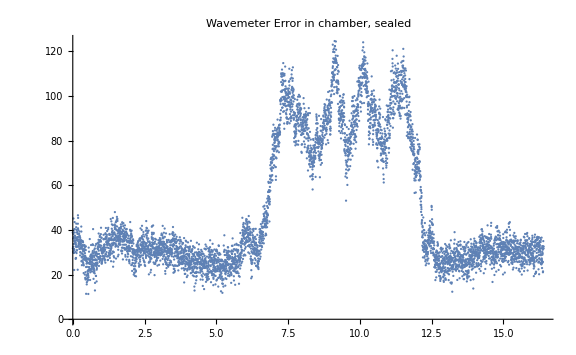

```mathematica
ListPlot[Transpose@{timeS/3600,1000(c3S-508848.92)},PlotLabel->"Wavemeter Error\n in chamber, sealed",FrameLabel->{"Time (hour)","Frequency (MHz)"},ImageSize->Large]
```

```mathematica
importTHP=Transpose[Import["/Users/gabrielpatenotte/Desktop/Wavemeter 8-starts-2021-11-15-16-23-00-ends-2021-11-15-21-11-11.csv",{"Data",2;;240}]];
Print[StringForm["The first data point occurs at ``, last at ``",importTHP[[1,1]],importTHP[[1,-1]]]]
timeTHP=AbsoluteTime/@importTHP[[1]];
timeTHP=timeTHP-timeTHP[[1]];
```

The first data point occurs at 2021-11-15 16:23:00, last at 2021-11-15 20:21:00

```mathematica
{T,H,P}=importTHP[[2;;-1]];
ftoC[x_]=(x-32)5/9+273.15;
T=Map[ftoC,T];
P=25.4*P;
```

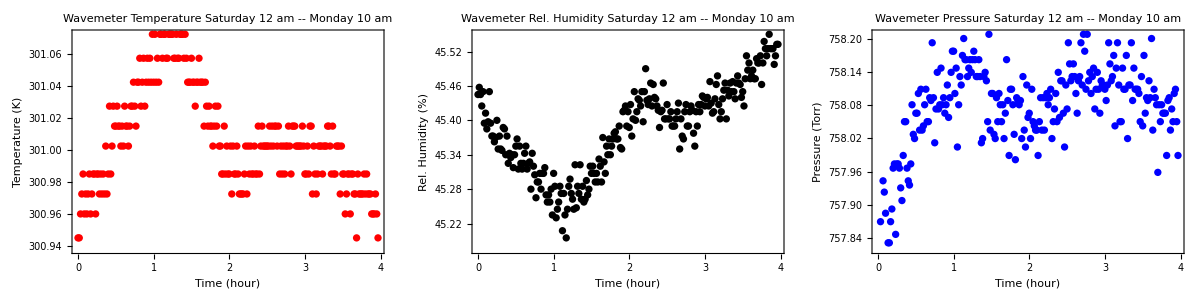

```mathematica
TableForm[{Table[ListPlot[Transpose@{timeTHP/3600,x[[1]]},ImageSize->Large,PlotStyle->x[[2]],PlotLabel-> StringForm["Wavemeter ``\n Saturday 12 am -- Monday 10 am",x[[3]]],FrameLabel->{"Time (hour)",x[[3]]<>x[[4]]}],{x,{{T,Red,"Temperature"," (K)"},{H,Black,"Rel. Humidity"," (%)"},{P,Blue, "Pressure"," (Torr)"}}}]}]
```

```mathematica
TableForm[{{ListPlot[Table[Transpose@{timeTHP/3600,(x-x[[-1500]])/x[[-1500]]},{x,{T,P}}],ImageSize->Large,PlotLegends->{"ΔT","ΔP"},PlotLabel->"Fractional change of T and P\n Saturday 12 am -- Monday 10 am",FrameLabel->{"Time (hour)","(x-x_0)/x_0"}],ListPlot[T/P,ImageSize->Large,PlotStyle->Purple,PlotLabel->"Difference between T and P\n Saturday 12 am -- Monday 10 am",FrameLabel->{"Time (hour)","T-P"}]}}]
```

```mathematica
Correlation[c3S-508848.92,P/T]
```

-0.188985

```mathematica
Length[Range[2,130800,549]]
```

239

```mathematica
1000(-1.95029698007176*^-6 (c3S-508848.92)[[1]])
```

-0.0000707595

```mathematica
(1.95029698007176*^-6 c6S[[40]])
```

0.920849

```mathematica
Mean[(c6S-(1.95029698007176*^-6 c6S[[2]])(c3S-508848.92))]
```

472155.

```mathematica
c6S[[2]]
```

472158.

```mathematica
1/c3S[[2]]
```

1.96522×10^-6

```mathematica
Correlation[1000((c6S[[2;;]]-(1.95029698007176*^-6 c6S[[2]])(c3S[[2;;]]-508848.92))-Mean[(c6S[[2;;]]-(1.95029698007176*^-6 c6S[[2]])(c3S[[2;;]]-508848.92))]),1000((c4S[[2;;]]-(1.95029698007176*^-6 c4S[[2]])(c3S[[2;;]]-508848.92))-Mean[(c4S[[2;;]]-(1.95029698007176*^-6 c4S[[2]])(c3S[[2;;]]-508848.92))])]
```

0.290033

```mathematica
StandardDeviation[1000((c5S[[2;;]]-(c5S[[2]]/c3S[[2]])(c3S[[2;;]]-508848.92))-Mean[(c5S[[2;;]]-(c5S[[2]]/c3S[[2]])(c3S[[2;;]]-508848.92))])]
```

0.936743

```mathematica
Manipulate[ListPlot[Transpose@{(timeS/3600)[[1+10;;-1-10]],1000((c6S[[1+10;;-1-10]]-α(1.95029698007176*^-6 c6S[[2]])MovingAverage[(c3S[[2;;]]-508848.92),20])-Mean[(c6S[[1+10;;-1-10]]-α(1.95029698007176*^-6 c6S[[2]])MovingAverage[(c3S[[2;;]]-508848.92),20])])},ImageSize->Large,ImagePadding-> {{70,10},{50,0}},PlotLabel->"correlation correction",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Red,AspectRatio->1,PlotRange->{-4,4}],{α,0,1}]
```

```mathematica
v=1
```

1

```mathematica
StandardDeviation[1000((c6S[[1+v;;-1-v]]-(1.95029698007176*^-6 c6S[[2]])MovingAverage[(c3S[[2;;]]-508848.92),2v])-Mean[(c6S[[1+v;;-1-v]]-(1.95029698007176*^-6 c6S[[2]])MovingAverage[(c3S[[2;;]]-508848.92),2v])])]
```

Part::take: Cannot take positions 41 through -41 in x.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

Part::take: Cannot take positions 41 through -41 in x.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

$Aborted

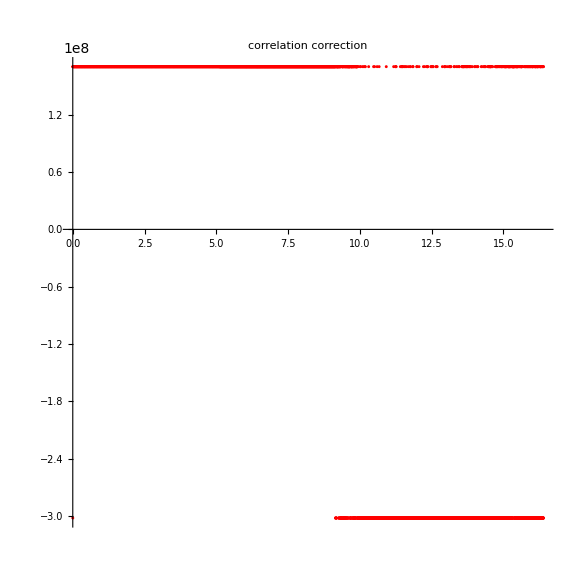
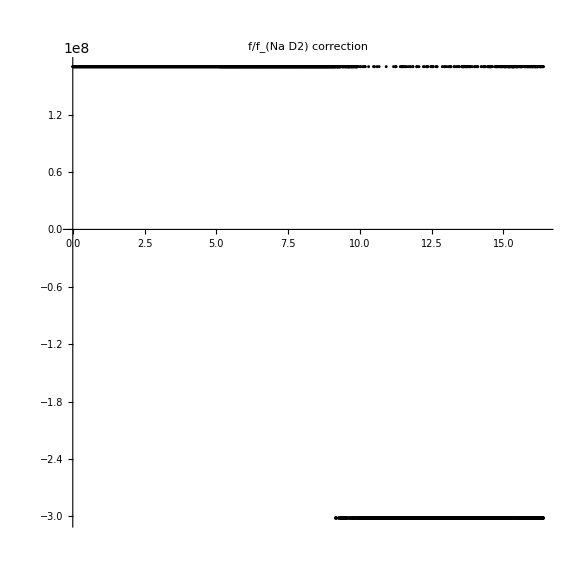
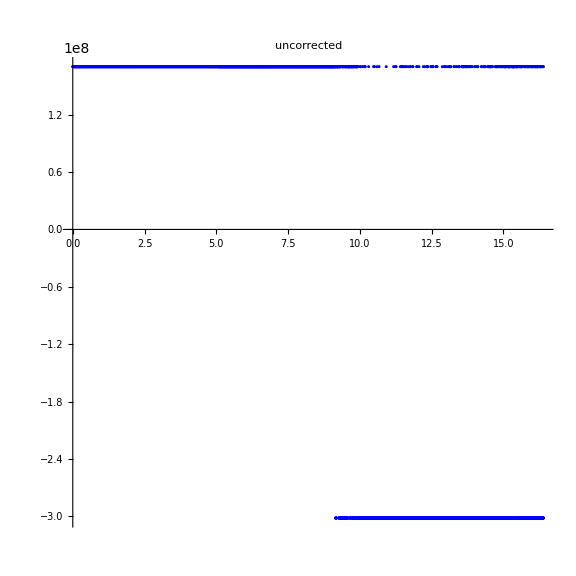

```mathematica
Table[{ListPlot[Transpose@{(timeS/3600)[[1;;-2]],1000(x[[1;;-2]]-(1.95029698007176*^-6 x[[2]])(c3S[[2;;]]-508848.92))-Mean[1000((x[[1;;-2]]-(1.95029698007176*^-6 x[[2]])(c3S[[2;;]]-508848.92)))]-36117},ImageSize->Large,ImagePadding-> {{70,10},{50,0}},PlotLabel->"correlation correction",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Red,AspectRatio->1],ListPlot[Transpose@{(timeS/3600)[[2;;]],1000((x[[2;;]]-(x[[2]]/c3S[[2]])(c3S[[2;;]]-508848.92))-Mean[(x[[2;;]]-(x[[2]]/c3S[[2]])(c3S[[2;;]]-508848.92))])},ImageSize->Large,ImagePadding-> {{70,10},{50,0}},PlotLabel->"f/f_(Na D2) correction",FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Black,AspectRatio->1],ListPlot[Transpose@{(timeS/3600)[[2;;]],1000(x[[2;;]]-Mean[(x[[2;;]])])},PlotLabel->"uncorrected",ImageSize->Large,ImagePadding-> {{70,10},{50,0}},FrameLabel->{"Time (hour)","Frequency (MHz)"},PlotStyle->Blue,AspectRatio->1]},{x,{c6S}}]
```

```mathematica
1/(1.95029698007176*^-6)
```

512742.

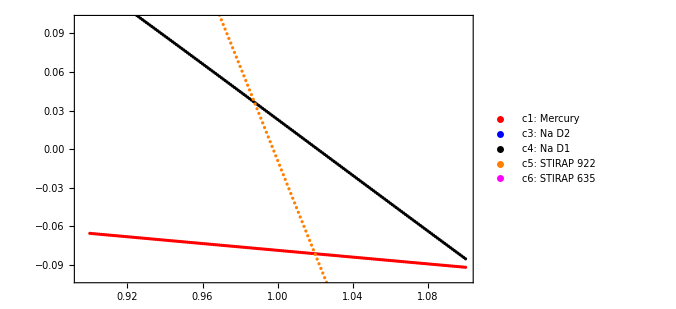

```mathematica
ListPlot[Table[Table[{α,Correlation[x[[2;;]]-(1.95029698007176*^-6 x[[1]])α (c3S[[2;;]]-508848.92),(c3S[[2;;]]-508848.92)]},{α,.9,1.1,.001}],{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->500,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"},PlotRange->{-0.1,.1}]//Quiet
```

```mathematica
Table[x[[2]],{x,{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}}]
Table[3 10^8/x[[2]],{x,{c1S,c2S,c3S,c4S,c5S,c6S,c7S,c8S}}]//Quiet
```

{353534.,0,508849.,508333.,325122.,472158.,0,328966.}

{848.575,ComplexInfinity,589.566,590.165,922.731,635.38,ComplexInfinity,911.948}

```mathematica
ListPlot[x[[2;;]]-.45 (c3S[[2;;]]-508848.92)
```

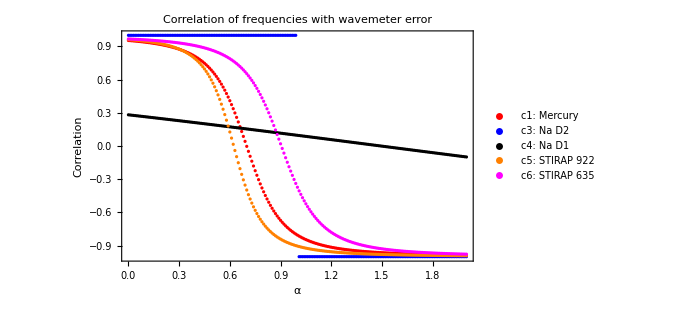

```mathematica
ListPlot[Table[Table[{α,Correlation[x[[2;;2950]]-α (c3S[[2;;2950]]-508848.92),(c3S[[2;;2950]]-508848.92)]},{α,0,2,.01}],{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->500,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"},FrameLabel->{"α","Correlation"},PlotLabel->"Correlation of frequencies with wavemeter error"]//Quiet
```

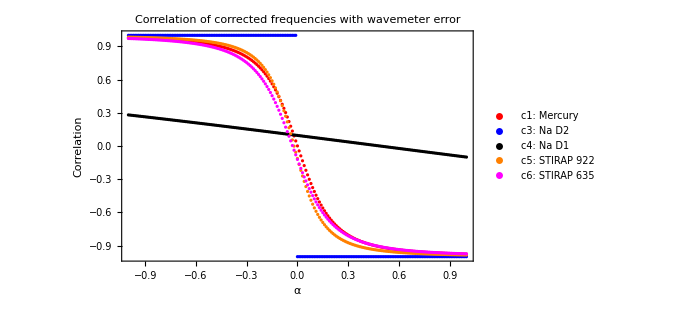

```mathematica
ListPlot[Table[Table[{α,Correlation[x[[2;;2950]]-(1.9775412404860485*^-6  x[[2]]) (c3S[[2;;2950]]-508848.92)-α (c3S[[2;;2950]]-508848.92),(c3S[[2;;2950]]-508848.92)]},{α,-1,1,.01}],{x,{c1S,c3S,c4S,c5S,c6S}}],ImageSize->500,PlotLegends->{"c1: Mercury","c3: Na D2","c4: Na D1","c5: STIRAP 922","c6: STIRAP 635"},FrameLabel->{"α","Correlation"},PlotLabel->"Correlation of corrected frequencies with wavemeter error"]//Quiet
```

```mathematica
data=Table[{x[[2]],MinimalBy[Table[{α,Correlation[x[[2;;1000]]-α (c3S[[2;;1000]]-508848.92),(c3S[[2;;1000]]-508848.92)]^2},{α,0,2,.001}],Last][[All,1]][[1]]},{x,{c1S,c3S,c4S,c5S,c6S}}];
lm=LinearModelFit[data,x,x,IncludeConstantBasis->False]
lm["RSquared"]
Show[ListPlot[data],Plot[lm[x],{x,0,6 10^5}],Frame->True,ImageSize->Large,FrameLabel-> {"Frequency (GHz)","Optimal α"},ImageSize-> Large]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

FittedModel[1.97754×10^-6 x]

```mathematica
1/c3S[[2]]
```

1.96522×10^-6

```mathematica
(1.3271693327807017*^-8)/(1.9775412404860485*^-6)
```

0.00671121

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 1.97754×10^-6 | 1.32717×10^-8 | 149.004 | 1.21681×10^-8

```mathematica
1/(1.9775412404860485*^-6)
```

505678.

```mathematica
1/(1.9252839662297696*^-6)
```

519404.

```mathematica
lm[{"MeanPredictionConfidenceIntervalTable","SinglePredictionConfidenceIntervalTable"}]
```

{Observed | Predicted | Standard Error | Confidence Interval
0.699 | 0.689496 | 0.00432704 | {0.677482,0.70151}
0.999 | 0.992407 | 0.006228 | {0.975115,1.0097}
1. | 0.9914 | 0.00622168 | {0.974125,1.00867}
0.623 | 0.634084 | 0.00397929 | {0.623036,0.645132}
0.905 | 0.920849 | 0.00577893 | {0.904804,0.936894},Observed | Predicted | Standard Error | Confidence Interval
0.699 | 0.689496 | 0.0128131 | {0.653921,0.725071}
0.999 | 0.992407 | 0.0135735 | {0.954721,1.03009}
1. | 0.9914 | 0.0135706 | {0.953722,1.02908}
0.623 | 0.634084 | 0.0126998 | {0.598824,0.669345}
0.905 | 0.920849 | 0.0133734 | {0.883718,0.957979}}

```mathematica
Table[(x[[2;;2950]]-(1.9775412404860485*^-6  x[[2]]) (c3S[[2;;2950]]-508848.92))[[2]],{x,{c1S,c3S,c4S,c5S,c6S,c8S}}]//FullForm
```

List[353534.,508849.,508333.,325122.,472158.,328966.]

```mathematica
1.3271693327807017*^-8*353533.9108219233*50
```

0.2346